```mathematica
Quit[]
ClearAll
```

```mathematica
(*This mathematica script produces all the plots on figure 6 of arXiv:2306.03893.*)
(*NB: All the equation numbers come from arXiv:2306.03893*)
(*NB: These script produces some computational errors. These are because of the breakdown of numercial methods (e.g. NIntegrate) in the unphysical region and the lack of precise tests to exclude them. Therrefore, it does not influence the physical results of the paper.*)
```

## Data

```mathematica
(*These parameters come from a script written by Fedor Bezrukov. This computes the running of the Standard Model coupling using the MS-Bar Scheme. It uses 2 loop matching of physical and MS-Bar parameters and 3 loop evolution of the coupling constants. As an input, it uses Subscript[α, s][Subscript[M, Z]] = 0.1181 and Subscript[m, h] = 125.1 GeV. It also neglected the running of ξ.*)
Vector = {{mt0->170.86894391716984,Yt0->0.9227764977382905,λ0->1.4839768164904959*^-6,b->0.000023962979354137353,q->0.3421368655721696},{mt0->170.86894392716985,Yt0->0.9227764977966643,λ0->1.4839127376880182*^-6,b->0.000023962979373887468,q->0.342136865409278},{mt0->170.86894393716983,Yt0->0.9227764978550346,λ0->1.4838486719888895*^-6,b->0.000023962979393632518,q->0.3421368652461153},{mt0->170.86894394716984,Yt0->0.9227764979134021,λ0->1.4837846190450932*^-6,b->0.00002396297941337242,q->0.34213686508266533},{mt0->170.86894395716985,Yt0->0.9227764979717714,λ0->1.4837205599203873*^-6,b->0.00002396297943311495,q->0.34213686491932943},{mt0->170.86894396716986,Yt0->0.9227764980301402,λ0->1.4836565000698813*^-6,b->0.000023962979452857658,q->0.34213686475601446},{mt0->170.86894397716983,Yt0->0.9227764980885074,λ0->1.48359244779037*^-6,b->0.000023962979472597598,q->0.34213686459251647},{mt0->170.86894398716984,Yt0->0.9227764981468751,λ0->1.4835283950309957*^-6,b->0.000023962979492337548,q->0.3421368644290205},{mt0->170.86894399716985,Yt0->0.9227764982052471,λ0->1.4834643225374172*^-6,b->0.00002396297951208524,q->0.34213686426604384},{mt0->170.86894400716983,Yt0->0.922776498263613,λ0->1.4834002764273622*^-6,b->0.0000239629795318225,q->0.3421368641024113},{mt0->170.86894401716984,Yt0->0.922776498321988,λ0->1.4833361915685143*^-6,b->0.000023962979551575187,q->0.3421368639396947},{mt0->170.86894402716985,Yt0->0.9227764983803555,λ0->1.48327213855076*^-6,b->0.000023962979571315283,q->0.3421368637762333},{mt0->170.86894403716985,Yt0->0.9227764984387213,λ0->1.4832080926809306*^-6,b->0.00002396297959105252,q->0.34213686361262374},{mt0->170.86894404716983,Yt0->0.9227764984970904,λ0->1.483144032916707*^-6,b->0.000023962979610795218,q->0.3421368634492955},{mt0->170.86894405716984,Yt0->0.9227764985554654,λ0->1.4830799479194115*^-6,b->0.000023962979630548036,q->0.3421368632865525},{mt0->170.86894406716985,Yt0->0.9227764986138266,λ0->1.483015920893257*^-6,b->0.00002396297965027771,q->0.3421368631225037},{mt0->170.86894407716986,Yt0->0.9227764986721988,λ0->1.4829518490521617*^-6,b->0.000023962979670025118,q->0.34213686295948226},{mt0->170.86894408716984,Yt0->0.9227764987305677,λ0->1.4828877900597141*^-6,b->0.00002396297968976765,q->0.3421368627961932},{mt0->170.86894409716984,Yt0->0.9227764987889383,λ0->1.482823724120247*^-6,b->0.000023962979709512906,q->0.34213686263299664},{mt0->170.86894410716985,Yt0->0.9227764988473042,λ0->1.4827596774590471*^-6,b->0.000023962979729250465,q->0.3421368624693923},{mt0->170.86894411716983,Yt0->0.9227764989056745,λ0->1.4826956121494168*^-6,b->0.000023962979748995308,q->0.3421368623061938},{mt0->170.86894412716984,Yt0->0.922776498964045,λ0->1.4826315461042633*^-6,b->0.000023962979768740506,q->0.34213686214304273},{mt0->170.86894413716985,Yt0->0.9227764990224097,λ0->1.4825675060669815*^-6,b->0.000023962979788475445,q->0.3421368619792855},{mt0->170.86894414716986,Yt0->0.9227764990807815,λ0->1.4825034343755701*^-6,b->0.000023962979808222856,q->0.34213686181620445},{mt0->170.86894415716984,Yt0->0.9227764991391489,λ0->1.4824393814373663*^-6,b->0.000023962979827962885,q->0.3421368616527383},{mt0->170.86894416716984,Yt0->0.922776499197521,λ0->1.4823753092067636*^-6,b->0.00002396297984771056,q->0.34213686148975686},{mt0->170.86894417716985,Yt0->0.9227764992558883,λ0->1.4823112570746906*^-6,b->0.000023962979867450338,q->0.34213686132627713},{mt0->170.86894418716983,Yt0->0.9227764993142589,λ0->1.4822471916427658*^-6,b->0.00002396297988719526,q->0.342136861163058},{mt0->170.86894419716984,Yt0->0.9227764993726262,λ0->1.4821831381645876*^-6,b->0.000023962979906935493,q->0.34213686099965446},{mt0->170.86894420716985,Yt0->0.9227764994309969,λ0->1.482119072697497*^-6,b->0.000023962979926680418,q->0.3421368608364298},{mt0->170.86894421716985,Yt0->0.9227764994893628,λ0->1.482055026056744*^-6,b->0.000023962979946418044,q->0.3421368606728429},{mt0->170.86894422716983,Yt0->0.9227764995477317,λ0->1.4819909668072027*^-6,b->0.00002396297996616055,q->0.34213686050952585},{mt0->170.86894423716984,Yt0->0.9227764996061069,λ0->1.4819268814627855*^-6,b->0.00002396297998591326,q->0.34213686034677726},{mt0->170.86894424716985,Yt0->0.9227764996644682,λ0->1.4818628549950838*^-6,b->0.000023962980005642926,q->0.34213686018271633},{mt0->170.86894425716983,Yt0->0.9227764997228385,λ0->1.4817987892807894*^-6,b->0.000023962980025388152,q->0.3421368600196032},{mt0->170.86894426716984,Yt0->0.9227764997812089,λ0->1.4817347238967671*^-6,b->0.00002396298004513294,q->0.3421368598563641},{mt0->170.86894427716985,Yt0->0.9227764998395797,λ0->1.4816706577618211*^-6,b->0.000023962980064878163,q->0.34213685969321217},{mt0->170.86894428716985,Yt0->0.9227764998979442,λ0->1.48160661842271*^-6,b->0.000023962980084612922,q->0.342136859529451},{mt0->170.86894429716983,Yt0->0.9227764999563143,λ0->1.4815425523951694*^-6,b->0.00002396298010435807,q->0.3421368593662886},{mt0->170.86894430716984,Yt0->0.9227765000146865,λ0->1.4814784800217048*^-6,b->0.000023962980124105803,q->0.34213685920320647},{mt0->170.86894431716985,Yt0->0.9227765000730523,λ0->1.481414434409712*^-6,b->0.000023962980143842847,q->0.34213685903959684},{mt0->170.86894432716986,Yt0->0.9227765001314245,λ0->1.4813503613263473*^-6,b->0.0000239629801635909,q->0.34213685887661316},{mt0->170.86894433716984,Yt0->0.9227765001897917,λ0->1.4812863091497344*^-6,b->0.00002396298018333061,q->0.3421368587131271},{mt0->170.86894434716984,Yt0->0.9227765002481608,λ0->1.4812222499852364*^-6,b->0.000023962980203073197,q->0.3421368585498192},{mt0->170.86894435716985,Yt0->0.9227765003065347,λ0->1.4811581706292597*^-6,b->0.00002396298022282347,q->0.34213685838697255},{mt0->170.86894436716983,Yt0->0.9227765003648973,λ0->1.4810941377594401*^-6,b->0.00002396298024255571,q->0.34213685822302986},{mt0->170.86894437716984,Yt0->0.9227765004232676,λ0->1.4810300722896113*^-6,b->0.00002396298026230069,q->0.34213685805982635},{mt0->170.86894438716985,Yt0->0.9227765004816383,λ0->1.4809660051767342*^-6,b->0.000023962980282046213,q->0.34213685789665493},{mt0->170.86894439716986,Yt0->0.922776500540001,λ0->1.4809019734090239*^-6,b->0.000023962980301778123,q->0.34213685773276276},{mt0->170.86894440716983,Yt0->0.9227765005983699,λ0->1.4808379136104531*^-6,b->0.000023962980321520784,q->0.34213685756946743},{mt0->170.86894441716984,Yt0->0.9227765006567467,λ0->1.4807738215257738*^-6,b->0.00002396298034127609,q->0.3421368574068591},{mt0->170.86894442716985,Yt0->0.9227765007151109,λ0->1.4807097823080892*^-6,b->0.00002396298036101075,q->0.3421368572431213},{mt0->170.86894443716983,Yt0->0.9227765007734782,λ0->1.4806457298478394*^-6,b->0.000023962980380750735,q->0.3421368570796233},{mt0->170.86894444716984,Yt0->0.9227765008318488,λ0->1.4805816637749743*^-6,b->0.00002396298040049591,q->0.34213685691644563},{mt0->170.86894445716985,Yt0->0.9227765008902177,λ0->1.4805176048447173*^-6,b->0.000023962980420238245,q->0.3421368567531443},{mt0->170.86894446716985,Yt0->0.9227765009485887,λ0->1.4804535388954757*^-6,b->0.00002396298043998349,q->0.34213685658997206},{mt0->170.86894447716983,Yt0->0.9227765010069574,λ0->1.4803894790662768*^-6,b->0.000023962980459725966,q->0.3421368564266158},{mt0->170.86894448716984,Yt0->0.9227765010653248,λ0->1.480325426788048*^-6,b->0.000023962980479465896,q->0.34213685626318985},{mt0->170.86894449716985,Yt0->0.9227765011236986,λ0->1.4802613481451196*^-6,b->0.000023962980499216082,q->0.34213685610030886},{mt0->170.86894450716983,Yt0->0.9227765011820658,λ0->1.4801972955255592*^-6,b->0.000023962980518956042,q->0.3421368559368355},{mt0->170.86894451716984,Yt0->0.9227765012404314,λ0->1.4801332496413118*^-6,b->0.00002396298053869343,q->0.3421368557732625},{mt0->170.86894452716984,Yt0->0.9227765012987972,λ0->1.480069203482936*^-6,b->0.00002396298055843063,q->0.342136855609618},{mt0->170.86894453716985,Yt0->0.9227765013571728,λ0->1.4800051173799058*^-6,b->0.000023962980578183808,q->0.3421368554468835},{mt0->170.86894454716983,Yt0->0.9227765014155415,λ0->1.4799410590435133*^-6,b->0.000023962980597925974,q->0.3421368552835532},{mt0->170.86894455716984,Yt0->0.9227765014739107,λ0->1.4798769993247303*^-6,b->0.00002396298061766857,q->0.342136855120226},{mt0->170.86894456716985,Yt0->0.9227765015322797,λ0->1.4798129398740483*^-6,b->0.000023962980637411184,q->0.34213685495690604},{mt0->170.86894457716986,Yt0->0.9227765015906515,λ0->1.479748867540654*^-6,b->0.00002396298065715897,q->0.34213685479388817},{mt0->170.86894458716984,Yt0->0.9227765016490158,λ0->1.479684828123754*^-6,b->0.00002396298067689365,q->0.34213685463013827},{mt0->170.86894459716984,Yt0->0.9227765017073849,λ0->1.4796207690363483*^-6,b->0.000023962980696636172,q->0.34213685446681597},{mt0->170.86894460716985,Yt0->0.9227765017657553,λ0->1.4795567031362249*^-6,b->0.00002396298071638124,q->0.34213685430365354},{mt0->170.86894461716983,Yt0->0.9227765018241227,λ0->1.4794926506046324*^-6,b->0.000023962980736121155,q->0.3421368541401177},{mt0->170.86894462716984,Yt0->0.9227765018824904,λ0->1.4794285974901382*^-6,b->0.00002396298075586124,q->0.34213685397665367},{mt0->170.86894463716985,Yt0->0.9227765019408624,λ0->1.4793645251907789*^-6,b->0.00002396298077560888,q->0.34213685381368913},{mt0->170.86894464716985,Yt0->0.9227765019992299,λ0->1.4793004724650372*^-6,b->0.00002396298079534893,q->0.3421368536502068},{mt0->170.86894465716983,Yt0->0.9227765020575985,λ0->1.4792364136462692*^-6,b->0.000023962980815091375,q->0.3421368534868704},{mt0->170.86894466716984,Yt0->0.9227765021159661,λ0->1.4791723609962076*^-6,b->0.000023962980834831186,q->0.34213685332339056},{mt0->170.86894467716985,Yt0->0.9227765021743335,λ0->1.4791083082825738*^-6,b->0.000023962980854571086,q->0.3421368531599398},{mt0->170.86894468716983,Yt0->0.9227765022327102,λ0->1.4790442156601249*^-6,b->0.00002396298087432671,q->0.3421368529973562},{mt0->170.86894469716984,Yt0->0.9227765022910774,λ0->1.4789801635386254*^-6,b->0.00002396298089406642,q->0.3421368528338822},{mt0->170.86894470716985,Yt0->0.9227765023494419,λ0->1.4789161236273233*^-6,b->0.000023962980913801413,q->0.34213685267012867},{mt0->170.86894471716985,Yt0->0.9227765024078141,λ0->1.4788520511834203*^-6,b->0.000023962980933548946,q->0.34213685250708203},{mt0->170.86894472716983,Yt0->0.9227765024661828,λ0->1.4787879928389088*^-6,b->0.00002396298095329124,q->0.3421368523437666},{mt0->170.86894473716984,Yt0->0.9227765025245489,λ0->1.4787239461471575*^-6,b->0.000023962980973028796,q->0.342136852180159},{mt0->170.86894474716985,Yt0->0.9227765025829193,λ0->1.478659880843174*^-6,b->0.000023962980992773927,q->0.34213685201695454},{mt0->170.86894475716983,Yt0->0.9227765026412881,λ0->1.4785958213820888*^-6,b->0.000023962981012516432,q->0.34213685185366793},{mt0->170.86894476716984,Yt0->0.9227765026996556,λ0->1.4785317687914896*^-6,b->0.000023962981032256287,q->0.3421368516901792},{mt0->170.86894477716984,Yt0->0.9227765027580279,λ0->1.4784676963990237*^-6,b->0.00002396298105200406,q->0.34213685152715345},{mt0->170.86894478716985,Yt0->0.9227765028163951,λ0->1.4784036434720446*^-6,b->0.000023962981071743967,q->0.34213685136370514},{mt0->170.86894479716983,Yt0->0.9227765028747639,λ0->1.4783395843387873*^-6,b->0.00002396298109148646,q->0.34213685120036746},{mt0->170.86894480716984,Yt0->0.9227765029331347,λ0->1.4782755180651345*^-6,b->0.00002396298111123184,q->0.34213685103720604},{mt0->170.86894481716985,Yt0->0.9227765029915035,λ0->1.4782114586987026*^-6,b->0.000023962981130974332,q->0.3421368508739025},{mt0->170.86894482716986,Yt0->0.9227765030498712,λ0->1.4781474063628044*^-6,b->0.00002396298115071396,q->0.3421368507104203},{mt0->170.86894483716983,Yt0->0.9227765031082399,λ0->1.4780833476201782*^-6,b->0.000023962981170456536,q->0.342136850547111},{mt0->170.86894484716984,Yt0->0.922776503166612,λ0->1.4780192748466648*^-6,b->0.000023962981190204462,q->0.34213685038406844},{mt0->170.86894485716985,Yt0->0.9227765032249765,λ0->1.4779552352771068*^-6,b->0.000023962981209939137,q->0.3421368502203319},{mt0->170.86894486716983,Yt0->0.9227765032833484,λ0->1.4778911625462657*^-6,b->0.000023962981229687057,q->0.34213685005731254},{mt0->170.86894487716984,Yt0->0.9227765033417158,λ0->1.4778271104796192*^-6,b->0.000023962981249426594,q->0.34213684989384724},{mt0->170.86894488716985,Yt0->0.9227765034000833,λ0->1.4777630578515148*^-6,b->0.000023962981269166483,q->0.3421368497303646},{mt0->170.86894489716985,Yt0->0.9227765034584537,λ0->1.4776989921252895*^-6,b->0.000023962981288911587,q->0.342136849567168},{mt0->170.86894490716983,Yt0->0.9227765035168258,λ0->1.47763491972658*^-6,b->0.00002396298130865939,q->0.34213684940412803},{mt0->170.86894492716985,Yt0->0.9227765036335578,λ0->1.4775068269165316*^-6,b->0.000023962981348134182,q->0.3421368490769225},{mt0->170.86894493716983,Yt0->0.9227765036919248,λ0->1.477442775445239*^-6,b->0.00002396298136787371,q->0.3421368489134328},{mt0->170.86894494716984,Yt0->0.9227765037503,λ0->1.4773786892699398*^-6,b->0.000023962981387626826,q->0.3421368487507127},{mt0->170.86894495716984,Yt0->0.9227765038086645,λ0->1.4773146496726031*^-6,b->0.000023962981407361667,q->0.3421368485869506},{mt0->170.86894496716985,Yt0->0.922776503867035,λ0->1.4772505832037377*^-6,b->0.000023962981427107028,q->0.3421368484238393},{mt0->170.86894497716983,Yt0->0.9227765039254008,λ0->1.4771865381090105*^-6,b->0.000023962981446843946,q->0.3421368482601446},{mt0->170.86894498716984,Yt0->0.9227765039837745,λ0->1.4771224586783416*^-6,b->0.00002396298146659447,q->0.3421368480973052},{mt0->170.86894499716985,Yt0->0.9227765040421448,λ0->1.4770583932840774*^-6,b->0.000023962981486339415,q->0.34213684793412563},{mt0->170.86894500716983,Yt0->0.9227765041005092,λ0->1.4769943536618808*^-6,b->0.00002396298150607411,q->0.3421368477703339},{mt0->170.86894501716984,Yt0->0.9227765041588829,λ0->1.4769302743935725*^-6,b->0.00002396298152582444,q->0.3421368476074696},{mt0->170.86894502716984,Yt0->0.9227765042172535,λ0->1.4768662086862697*^-6,b->0.000023962981545569522,q->0.3421368474443529},{mt0->170.86894503716985,Yt0->0.9227765042756175,λ0->1.4768021691703838*^-6,b->0.000023962981565304377,q->0.34213684728055105},{mt0->170.86894504716983,Yt0->0.9227765043339883,λ0->1.4767381034502063*^-6,b->0.000023962981585049504,q->0.34213684711734466},{mt0->170.86894505716984,Yt0->0.9227765043923573,λ0->1.4766740444659588*^-6,b->0.000023962981604791823,q->0.3421368469540285},{mt0->170.86894506716985,Yt0->0.9227765044507246,λ0->1.4766099920019058*^-6,b->0.000023962981624531763,q->0.3421368467905344},{mt0->170.86894507716985,Yt0->0.9227765045090923,λ0->1.4765459387477088*^-6,b->0.00002396298164427196,q->0.34213684662709865},{mt0->170.86894508716983,Yt0->0.922776504567464,λ0->1.4764818664714243*^-6,b->0.000023962981664019657,q->0.34213684646407333},{mt0->170.86894509716984,Yt0->0.922776504625833,λ0->1.4764178071980461*^-6,b->0.000023962981683762077,q->0.3421368463007441},{mt0->170.86894510716985,Yt0->0.9227765046842005,λ0->1.4763537546516709*^-6,b->0.000023962981703501926,q->0.34213684613730155},{mt0->170.86894511716983,Yt0->0.9227765047425739,λ0->1.476289676132983*^-6,b->0.000023962981723252095,q->0.34213684597442895},{mt0->170.86894512716984,Yt0->0.9227765048009383,λ0->1.4762256364253255*^-6,b->0.000023962981742986878,q->0.3421368458106343},{mt0->170.86894513716985,Yt0->0.9227765048593041,λ0->1.4761615901256401*^-6,b->0.000023962981762724345,q->0.34213684564702923},{mt0->170.86894514716985,Yt0->0.9227765049176795,λ0->1.4760975045334052*^-6,b->0.000023962981782477272,q->0.3421368454843215},{mt0->170.86894515716983,Yt0->0.9227765049760437,λ0->1.4760334654979002*^-6,b->0.00002396298180221169,q->0.3421368453205365},{mt0->170.86894516716984,Yt0->0.922776505034419,λ0->1.475969379452545*^-6,b->0.000023962981821964854,q->0.3421368451578063},{mt0->170.86894517716985,Yt0->0.9227765050927863,λ0->1.4759053269341085*^-6,b->0.000023962981841704723,q->0.34213684499433694},{mt0->170.86894518716983,Yt0->0.922776505151152,λ0->1.4758412810888233*^-6,b->0.000023962981861442105,q->0.3421368448306962},{mt0->170.86894519716984,Yt0->0.9227765052095196,λ0->1.475777228543928*^-6,b->0.00002396298188118188,q->0.3421368446672447},{mt0->170.86894520716984,Yt0->0.9227765052678932,λ0->1.4757131494925711*^-6,b->0.000023962981900932214,q->0.3421368445043627},{mt0->170.86894521716985,Yt0->0.9227765053262607,λ0->1.4756490962511168*^-6,b->0.000023962981920672364,q->0.342136844340936},{mt0->170.86894522716983,Yt0->0.9227765053846279,λ0->1.475585043787235*^-6,b->0.000023962981940412128,q->0.3421368441774883},{mt0->170.86894523716984,Yt0->0.9227765054429986,λ0->1.4755209781099372*^-6,b->0.000023962981960157306,q->0.3421368440142714},{mt0->170.86894524716985,Yt0->0.9227765055013675,λ0->1.475456919267909*^-6,b->0.0000239629819798996,q->0.3421368438509348},{mt0->170.86894525716983,Yt0->0.9227765055597394,λ0->1.4753928465426963*^-6,b->0.00002396298199964742,q->0.342136843687893},{mt0->170.86894526716983,Yt0->0.9227765056181022,λ0->1.47532881339163*^-6,b->0.00002396298201937973,q->0.3421368435240417},{mt0->170.86894527716984,Yt0->0.9227765056764744,λ0->1.4752647411299569*^-6,b->0.000023962982039127377,q->0.34213684336098066},{mt0->170.86894528716985,Yt0->0.9227765057348417,λ0->1.4752006881623485*^-6,b->0.000023962982058867416,q->0.3421368431975253},{mt0->170.86894529716983,Yt0->0.9227765057932107,λ0->1.475136629083066*^-6,b->0.000023962982078609873,q->0.3421368430342},{mt0->170.86894530716984,Yt0->0.9227765058515812,λ0->1.4750725633601302*^-6,b->0.000023962982098354896,q->0.34213684287104174},{mt0->170.86894531716985,Yt0->0.9227765059099517,λ0->1.4750084976923042*^-6,b->0.000023962982118099986,q->0.34213684270787376},{mt0->170.86894532716985,Yt0->0.9227765059683208,λ0->1.4749444381968048*^-6,b->0.000023962982137842667,q->0.34213684254452015},{mt0->170.86894533716983,Yt0->0.922776506026688,λ0->1.474880385863714*^-6,b->0.000023962982157582428,q->0.342136842381},{mt0->170.86894534716984,Yt0->0.922776506085054,λ0->1.474816338918163*^-6,b->0.000023962982177320098,q->0.34213684221749163},{mt0->170.86894535716985,Yt0->0.9227765061434274,λ0->1.4747522611375368*^-6,b->0.000023962982197070037,q->0.34213684205456674},{mt0->170.86894536716983,Yt0->0.9227765062017935,λ0->1.474688214378388*^-6,b->0.000023962982216807493,q->0.3421368418909285},{mt0->170.86894537716984,Yt0->0.9227765062601654,λ0->1.4746241417229077*^-6,b->0.000023962982236555253,q->0.34213684172795955},{mt0->170.86894538716984,Yt0->0.9227765063185362,λ0->1.474560075997712*^-6,b->0.000023962982256300337,q->0.34213684156477614},{mt0->170.86894539716985,Yt0->0.9227765063769019,λ0->1.4744960303098328*^-6,b->0.000023962982276037627,q->0.3421368414011439},{mt0->170.86894540716983,Yt0->0.9227765064352675,λ0->1.4744319848740302*^-6,b->0.00002396298229577469,q->0.3421368412375134},{mt0->170.86894541716984,Yt0->0.922776506493638,λ0->1.4743679189247102*^-6,b->0.00002396298231551989,q->0.3421368410743244},{mt0->170.86894542716985,Yt0->0.9227765065520134,λ0->1.4743038332908953*^-6,b->0.00002396298233527273,q->0.34213684091162067},{mt0->170.86894543716983,Yt0->0.9227765066103759,λ0->1.4742398003368434*^-6,b->0.000023962982355004934,q->0.3421368407477457},{mt0->170.86894544716984,Yt0->0.9227765066687482,λ0->1.4741757273259128*^-6,b->0.000023962982374752863,q->0.3421368405846967},{mt0->170.86894545716984,Yt0->0.9227765067271174,λ0->1.4741116681089659*^-6,b->0.000023962982394495337,q->0.3421368404213462},{mt0->170.86894546716985,Yt0->0.9227765067854863,λ0->1.4740476091988247*^-6,b->0.000023962982414237704,q->0.3421368402580133},{mt0->170.86894547716983,Yt0->0.9227765068438535,λ0->1.473983556448165*^-6,b->0.000023962982433977756,q->0.3421368400945477},{mt0->170.86894548716984,Yt0->0.9227765069022242,λ0->1.4739194902965066*^-6,b->0.0000239629824537229,q->0.34213683993140653},{mt0->170.86894549716985,Yt0->0.9227765069605931,λ0->1.473855431349233*^-6,b->0.0000239629824734653,q->0.34213683976809095},{mt0->170.86894550716983,Yt0->0.9227765070189602,λ0->1.4737913788886168*^-6,b->0.000023962982493205223,q->0.3421368396046413},{mt0->170.86894551716983,Yt0->0.9227765070773264,λ0->1.473727332822499*^-6,b->0.000023962982512942446,q->0.3421368394409504},{mt0->170.86894552716984,Yt0->0.922776507135697,λ0->1.4736632669402482*^-6,b->0.000023962982532687638,q->0.3421368392777806},{mt0->170.86894553716985,Yt0->0.922776507194069,λ0->1.4735991944585163*^-6,b->0.000023962982552435456,q->0.3421368391147349},{mt0->170.86894554716983,Yt0->0.9227765072524317,λ0->1.4735351615758534*^-6,b->0.00002396298257216752,q->0.34213683895084696},{mt0->170.86894555716984,Yt0->0.9227765073108039,λ0->1.4734710895024873*^-6,b->0.00002396298259191509,q->0.34213683878778145},{mt0->170.86894556716985,Yt0->0.9227765073691743,λ0->1.4734070236278559*^-6,b->0.000023962982611660304,q->0.3421368386246964},{mt0->170.86894557716985,Yt0->0.9227765074275434,λ0->1.473342964117914*^-6,b->0.000023962982631402955,q->0.34213683846137316},{mt0->170.86894558716983,Yt0->0.9227765074859106,λ0->1.4732789120675251*^-6,b->0.000023962982651142624,q->0.3421368382979069},{mt0->170.86894559716984,Yt0->0.9227765075442845,λ0->1.473214832089326*^-6,b->0.000023962982670893396,q->0.3421368381350205},{mt0->170.86894560716985,Yt0->0.9227765076026535,λ0->1.4731507735282932*^-6,b->0.00002396298269063546,q->0.3421368379716527},{mt0->170.86894561716983,Yt0->0.922776507661019,λ0->1.4730867275257402*^-6,b->0.000023962982710372944,q->0.3421368378080713},{mt0->170.86894562716984,Yt0->0.922776507719385,λ0->1.4730226812735767*^-6,b->0.000023962982730110262,q->0.3421368376444196},{mt0->170.86894563716984,Yt0->0.9227765077777554,λ0->1.4729586156990093*^-6,b->0.00002396298274985526,q->0.34213683748125057},{mt0->170.86894564716985,Yt0->0.9227765078361259,λ0->1.4728945497022642*^-6,b->0.000023962982769600412,q->0.34213683731809147},{mt0->170.86894565716983,Yt0->0.9227765078944965,λ0->1.4728304839768196*^-6,b->0.00002396298278934558,q->0.34213683715491194},{mt0->170.86894566716984,Yt0->0.9227765079528654,λ0->1.4727664246092772*^-6,b->0.000023962982809087984,q->0.34213683699162933},{mt0->170.86894567716985,Yt0->0.9227765080112298,λ0->1.4727023850295273*^-6,b->0.000023962982828822933,q->0.3421368368278766},{mt0->170.86894568716983,Yt0->0.9227765080696018,λ0->1.4726383129019907*^-6,b->0.00002396298284857051,q->0.3421368366648126},{mt0->170.86894569716983,Yt0->0.9227765081279707,λ0->1.4725742531867845*^-6,b->0.00002396298286831318,q->0.3421368365015016},{mt0->170.86894570716984,Yt0->0.9227765081863396,λ0->1.472510194731805*^-6,b->0.0000239629828880554,q->0.34213683633817},{mt0->170.86894571716985,Yt0->0.9227765082447072,λ0->1.4724461417895256*^-6,b->0.0000239629829077955,q->0.3421368361747089},{mt0->170.86894572716983,Yt0->0.9227765083030791,λ0->1.4723820697218448*^-6,b->0.000023962982927542956,q->0.34213683601166434},{mt0->170.86894573716984,Yt0->0.9227765083614496,λ0->1.4723180032764024*^-6,b->0.0000239629829472882,q->0.34213683584848514},{mt0->170.86894574716985,Yt0->0.9227765084198142,λ0->1.4722539640074568*^-6,b->0.000023962982967023047,q->0.34213683568472397},{mt0->170.86894575716983,Yt0->0.9227765084781859,λ0->1.4721898912610201*^-6,b->0.00002396298298677079,q->0.3421368355217595},{mt0->170.86894576716983,Yt0->0.9227765085365506,λ0->1.4721258522352615*^-6,b->0.00002396298300650553,q->0.3421368353579019},{mt0->170.86894577716984,Yt0->0.922776508594921,λ0->1.4720617862166822*^-6,b->0.00002396298302625044,q->0.34213683519470056},{mt0->170.86894578716985,Yt0->0.922776508653293,λ0->1.4719977137315693*^-6,b->0.000023962983045998264,q->0.34213683503172987},{mt0->170.86894579716983,Yt0->0.9227765087116604,λ0->1.4719336609531958*^-6,b->0.00002396298306573839,q->0.3421368348683094},{mt0->170.86894580716984,Yt0->0.9227765087700261,λ0->1.4718696157841624*^-6,b->0.00002396298308547526,q->0.3421368347046361},{mt0->170.86894581716984,Yt0->0.9227765088283965,λ0->1.471805550334626*^-6,b->0.00002396298310522033,q->0.34213683454147337},{mt0->170.86894582716985,Yt0->0.9227765088867659,λ0->1.471741490342424*^-6,b->0.00002396298312496303,q->0.3421368343781565},{mt0->170.86894583716983,Yt0->0.9227765089451394,λ0->1.4716774110516753*^-6,b->0.000023962983144713557,q->0.34213683421527535},{mt0->170.86894584716984,Yt0->0.9227765090035085,λ0->1.4716133514883419*^-6,b->0.000023962983164456062,q->0.342136834051973},{mt0->170.86894585716985,Yt0->0.9227765090618696,λ0->1.4715493254193638*^-6,b->0.000023962983184185564,q->0.3421368338879329},{mt0->170.86894586716983,Yt0->0.9227765091202448,λ0->1.4714852401672429*^-6,b->0.00002396298320393838,q->0.34213683372521286},{mt0->170.86894587716984,Yt0->0.922776509178609,λ0->1.4714212010545874*^-6,b->0.000023962983223672976,q->0.34213683356139774},{mt0->170.86894588716984,Yt0->0.9227765092369778,λ0->1.4713571418384788*^-6,b->0.000023962983243415386,q->0.3421368333980977},{mt0->170.86894589716985,Yt0->0.9227765092953455,λ0->1.4712930879958382*^-6,b->0.000023962983263155875,q->0.3421368332346477},{mt0->170.86894590716983,Yt0->0.9227765093537208,λ0->1.4712290029291873*^-6,b->0.0000239629832829085,q->0.34213683307191955},{mt0->170.86894591716984,Yt0->0.9227765094120882,λ0->1.4711649502788552*^-6,b->0.000023962983302648525,q->0.3421368329084244}};
```

## Scan Over yt0

```mathematica
(*This make the scan over the top yukawa and produces half of figure 6.*)
```

```mathematica
Dat = {}; CMB = {}; Xi = {}; Ratio = {}; Spect = {}; Init = {};
For[i=1,i<=Length[Vector],i++,
(*Extraction of parameters*)
Clear[λ0,q,b];
FitParam = Vector[[i]];

λ0 = λ0/.FitParam[[3]];b = b/.FitParam[[4]];q = q/.FitParam[[5]];yt = 0.43;
(*First Necessary Condition for jumpless, eq (4.8).*)
ξmax =  ((yt/q)/(Exp[1/4 (-1+Sqrt[1-16λ0/b])]))^2;
(*Second necessary condition for jumpless, eq (4.5).*)
If[λ0<=b/16,Jumpless =True;,Jumpless=False;];
If[Jumpless==True,
(*Analytical Solution for Loc Max Location*)
χminus[ξ1_] = 1/Sqrt[ξ1] ArcTanh[Sqrt[ξ1] q/yt Exp[-1/4(1+Sqrt[1-16 λ0/b])]];
(*Functions of the theory.*)
F[χ1_,ξ1_]= 1/Sqrt[ξ1] Tanh[Sqrt[ξ1]χ1];(*Palatini F, eq (3.11).*)
μ[χ1_,ξ1_]= yt F[χ1,ξ1];(*Energy scale as the top mass, eq(3.26).*)
λ[χ1_,ξ1_]= λ0 + b Log[μ[χ1,ξ1]/q]^2;(*SM running as function of the scale, eq (3.22)*)
U[χ1_,ξ1_]= 1/4 λ[χ1,ξ1] F[χ1,ξ1]^4;(*Full potential, eq (3.31)*)
dU[χ1_,ξ1_]= D[U[χ1,ξ1],χ1];
ϵSR[χ1_,ξ1_]= 1/2(dU[χ1,ξ1]/U[χ1,ξ1])^2;(*SLow roll parameter in order to define the initial condition.*)
(*Adjust ξmax such that the potential is globally increasing.*)
While[ξmax>0,
T = Table[U[x,ξmax],{x,$MachineEpsilon,4/Sqrt[ξmax],0.01/Sqrt[ξmax]}];
If[Max[T]- T[[Length[T]]]>0,ξmax=ξmax-0.01,Break[]];
];
ξ = ξmax;
Fin = False;
While[Fin == False,
ξ = ξ-0.01;
χi = 5/Sqrt[ξ]; L = 1000/Sqrt[ξ];
dχi = -Sqrt[2ϵSR[χi,ξ]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ]/U[y[Ne],ξ]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
Nmax = Nup;
While[Im[χsol[Nmax]]!=0,
Nmax = Nmax -0.01;
];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ]/(6-(χsol'[x1])^2)];
Fin = False;
If[Max[Table[Re[ϵ[x]],{x,0,Nmax,Nmax/10000}]]>=1,Fin = True;];];
d = Abs[Nup -55];
T =If[d < 5, Table[{ϵ[x]-1,x},{x,Nup-d,Nup,0.001}],Table[{ϵ[x]-1,x},{x,Nup-d,Nup,0.005}]];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
Enh =Log10[ Max[Table[Pζ[x],{x,NCMB,Nend,0.1}]]/Pζ[NCMB]];
ηCMB =(D[dU[x,ξ],x]/.x->χsol[NCMB])/U[χsol[NCMB],ξ];
ϵCMB = ϵ[χsol[NCMB]];
(*ns_PLANCK = 0.9603±0.0073*)
ns = 1-6ϵCMB +2ηCMB;
(*PCMB_PLANCK = 2.1*^-9*)
r = 16ϵCMB;
AppendTo[Dat,{λ0,Enh}];
AppendTo[CMB,{λ0,Pζ[NCMB]}];
AppendTo[Spect,{λ0,ns}];
AppendTo[Ratio,{λ0,r}];
AppendTo[Xi,{λ0,ξ}];
AppendTo[Init,{λ0,χsol[NCMB]}];
(*Hilltop Test*)
If[Re[χsol[NCMB]]<= χminus[ξ],Hilltop = True; Break[],Hilltop = False;]
];
]
```

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 360..

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 336.913.

NDSolveValue::mxst: Maximum number of 10000 steps reached at the point Ne == 336.688.

General::stop: Further output of NDSolveValue::mxst will be suppressed during this calculation.

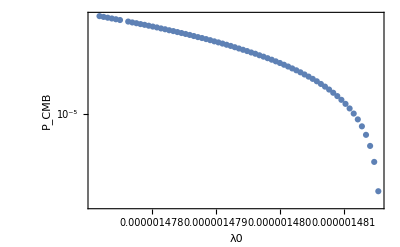

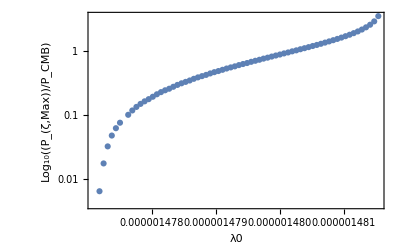

```mathematica
RelCMB = {};
For[i=1,i<=Length[Dat],i++,
If[Dat[[i]][[2]]>0,AppendTo[RelCMB,CMB[[i]]]];
]
RelSpect = {};
For[i=2,i<=Length[Dat],i++,
If[Dat[[i]][[2]]>0,AppendTo[RelSpect,Spect[[i]]]];
]
(*Only Plot for the points where the enhancement is non zero.*)
plot1 = ListLogPlot[RelCMB,Frame->True,(*Joined->True,*)FrameLabel->{"λ0",Subscript[P,"CMB"]},FrameStyle->Black]
plot2 = ListLogPlot[Dat,Frame->True,(*Joined->True,*)FrameLabel->{"λ0",Subscript[Log,10][Subscript[P,"ζ,Max"]/Subscript[P,"CMB"]]},FrameStyle->Black]
```

## Minimal CMB

```mathematica
(*This focuses on the minimal CMB power spectrum and produces the remaing half of figure 6.*)
```

```mathematica
CMB2 = {};
For[i=1,i<=Length[CMB],i++, AppendTo[CMB2,{CMB[[i]][[2]]}]];
For[i=1, i<=Length[CMB],i++,If[CMB2[[i]] == {Min[CMB2]},Rank = i]];
Clear[λ0,b,q];
FitParam = Vector[[Rank]];
λ0 = λ0/.FitParam[[3]];b = b/.FitParam[[4]];q = q/.FitParam[[5]];yt = 0.43;
(*First Necessary Condition for jumpless*)
ξmax =  ((yt/q)/(Exp[1/4 (-1+Sqrt[1-16λ0/b])]))^2;
(*Second necessary condition for jumpless*)
If[λ0<=b/16,Jumpless =True;,Jumpless=False;];
If[Jumpless==True,
(*Analytical Solution for Loc Max Location*)
χminus[ξ1_] = 1/Sqrt[ξ1] ArcTanh[Sqrt[ξ1] q/yt Exp[-1/4(1+Sqrt[1-16 λ0/b])]];
(*Definition of the Potential*)
F[χ1_,ξ1_]= 1/Sqrt[ξ1] Tanh[Sqrt[ξ1]χ1];
μ[χ1_,ξ1_]= yt F[χ1,ξ1];
λ[χ1_,ξ1_]= λ0 + b Log[μ[χ1,ξ1]/q]^2;
U[χ1_,ξ1_]= 1/4 λ[χ1,ξ1] F[χ1,ξ1]^4;
dU[χ1_,ξ1_]= D[U[χ1,ξ1],χ1];
ϵSR[χ1_,ξ1_]= 1/2(dU[χ1,ξ1]/U[χ1,ξ1])^2;
(*Adjust ξmax such that the potential is globally increasing.*)
While[ξmax>0,
T = Table[U[x,ξmax],{x,$MachineEpsilon,4/Sqrt[ξmax],0.01/Sqrt[ξmax]}];
If[Max[T]- T[[Length[T]]]>0,ξmax=ξmax-0.01,Break[]];
];
ξ = ξmax;
Fin = False;
While[Fin == False,
ξ = ξ-0.01;
χi = 5/Sqrt[ξ]; L = 1000/Sqrt[ξ];
dχi = -Sqrt[2ϵSR[χi,ξ]];
χsol =NDSolveValue[{y''[Ne] + 3 y'[Ne] -1/2 (y'[Ne])^3 + (3-1/2(y'[Ne])^2)dU[y[Ne],ξ]/U[y[Ne],ξ]==0,y[0]==χi, y'[0]==dχi},y,{Ne,$MachineEpsilon,L}];
Nup = ResourceFunction["InterpolatingFunctionDomain"][χsol][[1]][[2]];
Nmax = Nup;
While[Im[χsol[Nmax]]!=0,
Nmax = Nmax -0.01;
];
ϵ[x1_]= 1/2(χsol'[x1])^2;
H[x1_]=Sqrt[U[χsol[x1],ξ]/(6-(χsol'[x1])^2)];
Fin = False;
If[Max[Table[Re[ϵ[x]],{x,0,Nmax,Nmax/10000}]]>=1,Fin = True;];];
Δ = Abs[Nup -55];
T =If[Δ < 5, Table[{ϵ[x]-1,x},{x,Nup-Δ,Nup,0.001}],Table[{ϵ[x]-1,x},{x,Nup-Δ,Nup,0.005}]];
Laste = False;
For[a =1, a<=Length[T]-1, a++, 
If[Laste == False,If[Sign[T[[a]][[1]]]!= Sign[T[[a+1]][[1]]],A = a; Laste = True]]
];
Nend = T[[A]][[2]];
NCMB = Nend-55;
Pζ[Nfold_]= H[Nfold]^2/(8 Pi^2 ϵ[Nfold]);
Enh =Log10[ Max[Table[Pζ[x],{x,NCMB,Nend,0.1}]]/Pζ[NCMB]];
ηCMB =(D[dU[x,ξ],x]/.x->χsol[NCMB])/U[χsol[NCMB],ξ];
ϵCMB = ϵ[χsol[NCMB]];
(*ns_PLANCK = 0.9603±0.0073*)
ns = 1-6ϵCMB +2ηCMB;
(*PCMB_PLANCK = 2.1*^-9*)
r = 16ϵCMB;
]
TMukh = {};(* Empty List*)
TMukhValue = {};
Mp=2.4 10^18;(*GeV*)
HMpc[x1_] = H[x1] Mp 1.56 10^38; (*Mpc^-1*);
kcom[Ne1_]= (0.05 H[Ne1])/H[NCMB] E^(Ne1-NCMB);
Ne= Interpolation[Table[{kcom[x],x},{x,NCMB,Nend,0.01}]];
η[x1_] = ϵ[x1] - 0.5 ϵ'[x1]/ϵ[x1];
ascale[x1_] =(0.05 (*Mpc^-1*)/( HMpc[NCMB](*Mpc^-1*))) Exp[x1-NCMB];
Foo[x1_,k1_] = (k1/(kcom[x1]))^2+(1+ϵ[x1] - η[x1])(η[x1]-2)-(ϵ'[x1]-η'[x1]); 
M = 200; (*Number of Points*)
For[k=kcom[NCMB],k<kcom[Nend],k= k (kcom[Nend]/kcom[NCMB])^(1/M),
(*we go far in the horizon for the intial condition*)
If[k>100,ki = k/100,ki=kcom[NCMB]];
If[k>10^14, ki = k/10];
Ni = Ne[ki];
Ruin = 1/Sqrt[2 k]; dRuin = 0;(*Real Part of Bunch Davies Vacuum*)
Nf = Ne[k];
Rusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Ruin,f'[Ni]==dRuin},f,{x,Ni,Nf}];(*Real Part of MS*)
Iuin = 0; dIuin = -Sqrt[k/2]/ki;(*Imaginary part of Bunch Davies Vacuum*)
Iusol = NDSolveValue[{(f''[x]+ (1-ϵ[x])f'[x]+(Foo[x,k])f[x])==0,f[Ni]==Iuin,f'[Ni]==dIuin},f,{x,Ni,Nf}];(*Imaginary part of MS*)
uSquared = Rusol[Nf]^2 + Iusol[Nf]^2; (*Mpc, since we set the initial condition as fct of k in Mpc*)
z = -ascale[Nf]χsol'[Nf] Mp 1.56 10^38; (*Mpc^-1, the numerical factor is the conversion factor btw Mpc^-1 and GeV.*)
Pow = k^3 uSquared/((2π^2)z^2);(*Dimensionless*)
AppendTo[TMukh,{k,Pow}];
AppendTo[TMukhValue,{Pow}]]
q1 = ListLogLogPlot[TMukh,PlotStyle->Orange,Joined->True];
q2 = LogLogPlot[Pζ[Ne[x]],{x,kcom[NCMB],kcom[Nend]},PlotRange->All,Frame->True,FrameLabel->{"k["Superscript["Mpc]",-1],Subscript[P,R]["k"]},FrameStyle->Black];
plot4 = Show[q2,q1];
Show[q2,q1]
p1 = Plot[U[x,ξ],{x,0,4/Sqrt[ξ]},Frame->True,FrameLabel->{χ,U[χ]},FrameStyle->Black];
p2 = Plot[U[x,ξ],{x,χsol[NCMB],χsol[Nend]},PlotStyle->Red];
Show[p1,p2]
```